```mathematica
Solve[0.0012x+.8097==1,x]
```

{{x→158.583}}

```mathematica
Solve[0.0012x+.8097==0.967208659,x]
```

{{x→131.257}}

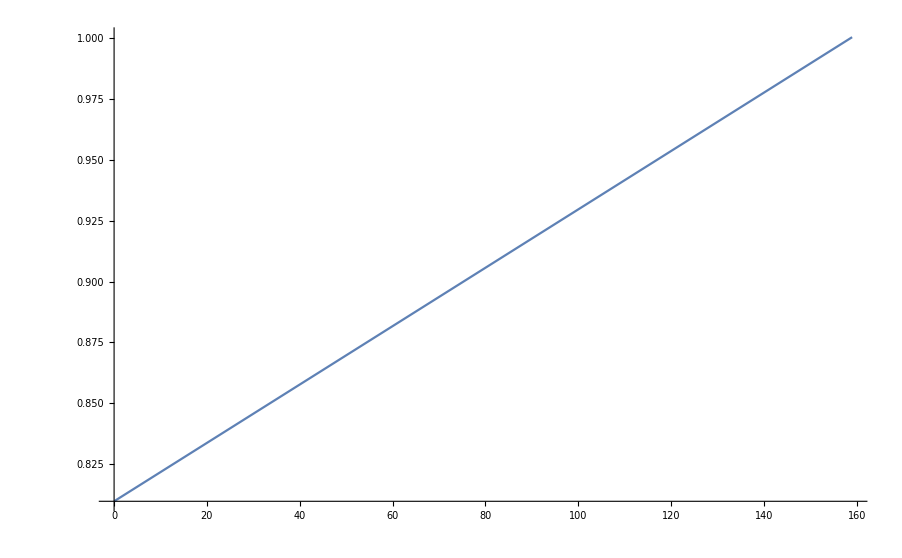

```mathematica
Plot[0.0012x+.8097,{x,0,159}]
```

```mathematica
85/131*158//N
```

102.519

```mathematica
a={71,90,122,179,207,288,320,273,257,412,535,490,575,629,545,478,553,584,568,504,499,358,314,490,459,462,421,393,270,242,250,310,320,303,265,232,172,263,211,210,217,202,127,123,174,178,152,128,77,59,84,116,98,108,75,83,60,43,70,81,67,65,60,43,50,58,71,56,34,48,27,39,36,49,27,29,40,25,26,31,21,32,26,21,23,16,24,19,32,23,12,17,11,24,19,20,20,18,10,12,12,16,19,18,16,5,13,17,9,13,5}
```

{71,90,122,179,207,288,320,273,257,412,535,490,575,629,545,478,553,584,568,504,499,358,314,490,459,462,421,393,270,242,250,310,320,303,265,232,172,263,211,210,217,202,127,123,174,178,152,128,77,59,84,116,98,108,75,83,60,43,70,81,67,65,60,43,50,58,71,56,34,48,27,39,36,49,27,29,40,25,26,31,21,32,26,21,23,16,24,19,32,23,12,17,11,24,19,20,20,18,10,12,12,16,19,18,16,5,13,17,9,13,5}

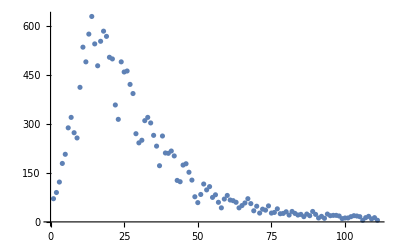

```mathematica
ListPlot[a]
```

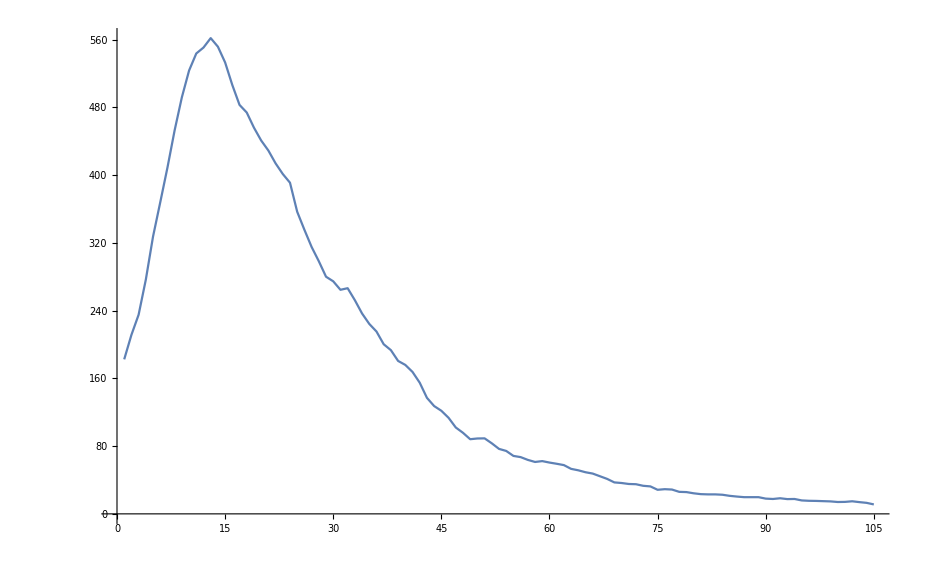

```mathematica
MovingAverage[a,7]//ListLinePlot
```

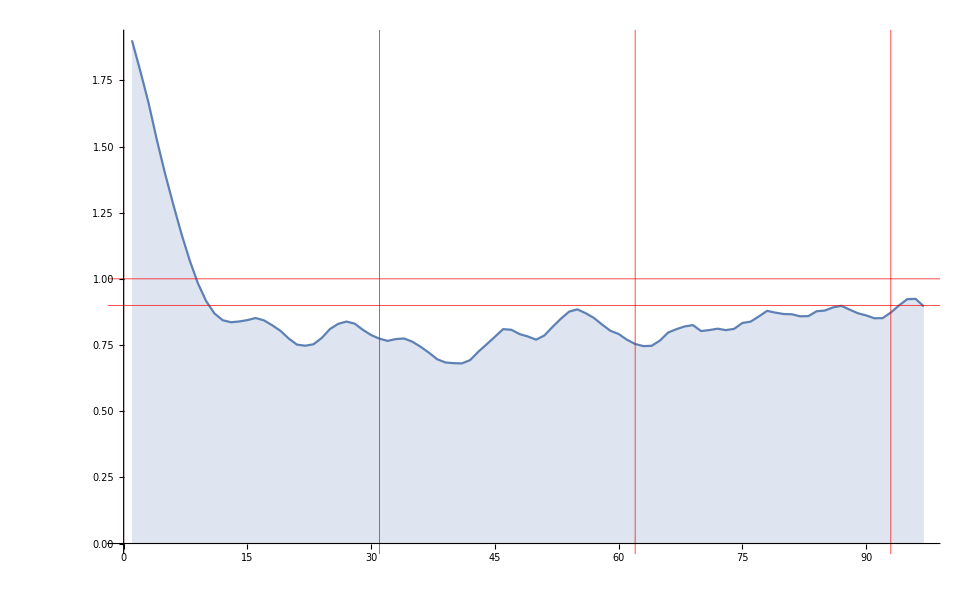

```mathematica
ListLinePlot[
With[{todo=MovingAverage[a,7]},
Table[Sum[todo[[5+k+i]],{i,0,3}]/Sum[todo[[k+i]],{i,0,3}],{k,Length[todo]-8}]
],GridLines->{{0,31,62,93}, {-1,0.9,1}},GridLinesStyle->Directive[Thick, Red],Filling->Axis, FillingStyle->Automatic, PlotRange->All
]
```